-Graphics-

```mathematica
k[a_,b_]:=KroneckerProduct[a,b](*shorthand Kronecker product*)
θ=π/2;(*angle between array and B-field*)
nM=1; (*maximum rotational angular momentum N*)
nS=Sum[2j+1,{j,0,nM}]; (*number of states in the Hilbert space*)
nP=2;(*number of particles that interact*)
h=IdentityMatrix[nS];(*single particle Hilbert space*)
hP=IdentityMatrix[nS^nP];(*multi-particle Hilbert space*)
s=Partition[h,{nS,1}][[1]];(*states in the single particle Hilbert space*)
sP=Partition[hP,{nS^nP,1}][[1]];(*states in the single particle Hilbert space*)
l=Flatten[Table[{n,m},{n,0,nM},{m,-n,n}],1];(*state labels |N,m⟩*)
lP=Flatten[Table[{{ni,mi},{nj,mj}},{ni,0,nM},{mi,-ni,ni},{nj,0,nM},{mj,-nj,nj}],3];(*multi-particle state labels |Subscript[N, i],Subscript[m, i],Subscript[N, j],Subscript[m, j]⟩*)
s2l=AssociationThread[s->l]; (*map between states in the single particle Hilbert space and their quantum numbers*)
l2s=AssociationThread[l->s]; 
s2lP=AssociationThread[sP->lP]; (*map between states in the multi-particle Hilbert space and their quantum numbers*)
dpME[q_,{Nb_,mb_},{Nk_,mk_}]:=Quiet[d (-1)^mb √((2 Nb+1) (2 Nk+1)) ThreeJSymbol[{Nb,-mb},{1,q},{Nk,mk}] ThreeJSymbol[{Nb,0},{1,0},{Nk,0}]](*dipole matrix element for spherical component q between bra Nm and ket Nm*)
HME[lb_,lk_]:=Module[{b1,b2,k1,k2},{b1,b2}=lb;{k1,k2}=lk;
(1-3 Cos[θ]^2)/r^3(dpME[0,b1,k1]dpME[0,b2,k2]+(dpME[1,b1,k1]dpME[-1,b2,k2]+dpME[-1,b1,k1]dpME[1,b2,k2])/2)](*Matrix element of the dipolar Hamiltonian*)
lr=Select[lP,(Abs[#[[1,1]]-#[[2,1]]]==1&&Abs[#[[1,2]]-#[[2,2]]]<=1)&];(*Selection rule for states with dipole-dipole interactions*)
(*lPr=Select[lPr,(#[[1,1]]*#[[1,2]]+#[[2,1]]*#[[2,2]])==0&];*) (*Additional, optional selection rule*)
nr=Length[lr]; (*Number of selected states*)
hr=IdentityMatrix[nr];(*Selected Hilbert space*)
sr=Partition[hr,{nr,1}][[1]];(*states in the selected Hilbert space*)
s2lr=AssociationThread[sr->lr]; (*map between states and quantum numbers*)
l2sr=AssociationThread[lr->sr]; (*map between states and quantum numbers*)
HDD=Sum[HME[lr[[nb]],lr[[nk]]]SparseArray[sr[[nb]].sr[[nk]]ᵀ],{nk,1,nr},{nb,1,nr}];(*Hamiltonian in the selected Hilbert space*)
sME2=(l2sr[{{0,0},{1,1}}]-l2sr[{{0,0},{1,-1}}])/(√2);sME1=(l2sr[{{1,1},{0,0}}]-l2sr[{{1,-1},{0,0}}])/(√2);
FullSimplify[(Abs[sME1ᵀ.MatrixExp[-ⅈ t HDD].sME2]^2)[[1,1]],Assumptions->{d>0,t>0,r>0}]
```

Sin[(d^2 t)/(6 r^3)]^2

```mathematica
sMEa=(-0.23533895684362188-0.666795002524581 ⅈ)l2sr[{{0,0},{1,-1}}]+(0.7071067811865475)l2sr[{{0,0},{1,1}}];
sMEb=(-0.23533895684362188-0.666795002524581 ⅈ)l2sr[{{1,-1},{0,0}}]+(0.7071067811865475)l2sr[{{1,1},{0,0}}];
```

```mathematica
FullSimplify[(Abs[(sMEb†.MatrixExp[-ⅈ t HDD].sMEa)]^2)[[1,1]],Assumptions->{d>0,t>0,r>0}]
```

1. Sin[(d^2 t)/(6 r^3)]^2

```mathematica
UnitConvert[1/(2π)(4.6 Debye)^2/(4π ϵ0 6 (2.7 um)^3 ℏ),Hz]
```

```mathematica
(d^2/(4π ϵ0 6 r^3 h))^-1
```

27.0406 Hz

```mathematica
UnitConvert[1/(37 ms)]//N
```

27.027 per second

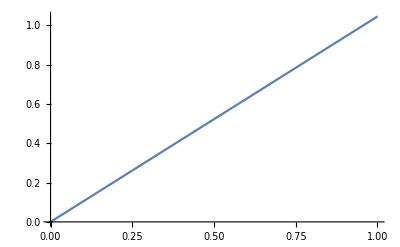

```mathematica
Plot[(4.6 Debye)^2/(6 (1.5 um)^3)t Quantity[1,"Seconds"],{t,0,1}]
```

```mathematica
θ=.;ϕ=.;Y1m=SphericalHarmonicY[1,-1,θ,ϕ];
Y1p=SphericalHarmonicY[1,1,θ,ϕ];
Y10=SphericalHarmonicY[1,0,θ,ϕ];
```

```mathematica
2 √(π/3)Y10
```

Cos[θ]

```mathematica
√((2π)/3)(Y1m-Y1p)//FullSimplify
```

Cos[ϕ] Sin[θ]

```mathematica
ⅈ √((2π)/3)(Y1m+Y1p)//FullSimplify
```

Sin[θ] Sin[ϕ]

```mathematica
e0={0,0,1};
em=1/(√2){1,ⅈ,0};
ep=1/(√2){-1,ⅈ,0};
```

```mathematica
T=√((4π)/3)SphericalHarmonicY[1,#,θ,ϕ]&/@{-1,0,1};
```

```mathematica
T[[1]]em+T[[2]]e0+T[[3]]ep//FullSimplify
```

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

```mathematica
d={dm,d0,dp};
```

```mathematica
Sum[(-1)^q d[[q+2]]T[[2-q]],{q,-1,1}]//FullSimplify
```

d0 Cos[θ]+(ⅇ^(-ⅈ ϕ) (-dp+dm ⅇ^(2 ⅈ ϕ)) Sin[θ])/(√2)

```mathematica
ThreeJSymbol[{1,0},{1,-1},{2,1}]
```

```mathematica
-(-√5)/(√10)
```

1/(√2)

```mathematica
√(2/15)/(1/(√30))
```

2

```mathematica
√(5/30)
```

1/(√6)

```mathematica
k1=1;k2=1;k=2;p=-2;
T=.;√6 Sum[T[k1,p1,A1]T[k2,p-p1,A2] √(2k+1)ThreeJSymbol[{k1,p1},{k2,p-p1},{k,-p}](-1)^(-k1+k2-p),{p1,-k1,k1}] √((4π)/5)Y[2,-p]//FullSimplify
```

3/2 ⅇ^(2 ⅈ ϕ) Sin[θ]^2 T[1,-1,A1] T[1,-1,A2]

```mathematica
√((4π)/3)Y[1,0]
```

Cos[θ]

```mathematica
FullSimplify[Sum[SphericalHarmonicY[1,g,θ1,ϕ1]*SphericalHarmonicY[1,g,θ2,ϕ2],{g,-1,1}],Assumptions->{θ1>0,ϕ1>0,θ2>0,ϕ2>0}]
```

(3 (Cos[θ1] Cos[θ2]+Cos[ϕ1-ϕ2] Sin[θ1] Sin[θ2]))/(4 π)

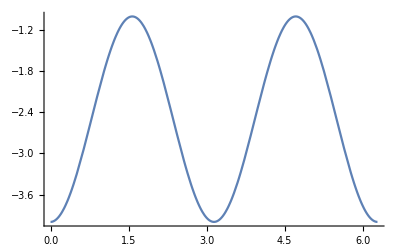

```mathematica
Plot[-4 Cos[θ]^2-Sin[θ]^2,{θ,0,2π}]
```

```mathematica
TrigReduce[2Cos[θ]Sin[θ]]
```

Sin[2 θ]

```mathematica
T
```

{(ⅇ^(-ⅈ ϕ) Sin[θ])/(√2),Cos[θ],-(ⅇ^(ⅈ ϕ) Sin[θ])/(√2)}

```mathematica
√((4π)/(2 2+1))SphericalHarmonicY[2,#,θ,ϕ]&/@Range[-2,2]
```

{1/2 √(3/2) ⅇ^(-2 ⅈ ϕ) Sin[θ]^2,√(3/2) ⅇ^(-ⅈ ϕ) Cos[θ] Sin[θ],1/2 (-1+3 Cos[θ]^2),-√(3/2) ⅇ^(ⅈ ϕ) Cos[θ] Sin[θ],1/2 √(3/2) ⅇ^(2 ⅈ ϕ) Sin[θ]^2}

```mathematica
Y[l_,m_]:=SphericalHarmonicY[l,m,θ,ϕ]
```

```mathematica
FullSimplify[√((4π r^2)/3){1/(√2)(Y[1,-1]-Y[1,1]),ⅈ/(√2)(Y[1,-1]+Y[1,1]),Y[1,0]},Assumptions->r>0]
```

{r Cos[ϕ] Sin[θ],r Sin[θ] Sin[ϕ],r Cos[θ]}

```mathematica
ϵ0={0,0,1};
ϵm=1/(√2){1,-ⅈ,0};
ϵp=-1/(√2){1,ⅈ,0};
```

```mathematica
√((4π)/3)(ϵ0* Y[1,0]+ϵm* Y[1,-1]+ϵp* Y[1,1])//FullSimplify
```

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

```mathematica
ϵp*.ϵp
```

1

```mathematica
√((4π)/3)Y[2,0]
```

1/2 √(5/3) (-1+3 Cos[θ]^2)

```mathematica
Off[ClebschGordan::phy];
```

```mathematica
With[{q=-2},1/Y[2,q] Sum[ClebschGordan[{1,q1},{1,q2},{2,q}]Y[1,q1]Y[1,q2],{q1,-1,1},{q2,-1,1}]]//Simplify
```

√(3/(10 π))

```mathematica
p1=.
```

```mathematica
With[{k=2,p=2,k1=1,k2=1},1/(√((4π)/(2(2)+1))Y[k,p])Sum[√((4π)/3)Y[1,p1] √((4π)/3)Y[1,p-p1](2k+1)^(1/2)ThreeJSymbol[{k1,p1},{k2,p-p1},{k,-p}](-1)^(-k1+k2-p),{p1,-1,1}]]//FullSimplify
```

√(2/3)

```mathematica
√((4π)/(2(2)+1))
```

2 √(π/5)

```mathematica
Sum[(-1)^p SphericalHarmonicY[1,p,θ1,ϕ1]SphericalHarmonicY[1,-p,θ2,ϕ2],{p,-2,2}]//FullSimplify
```

(3 (Cos[θ1] Cos[θ2]+Cos[ϕ1-ϕ2] Sin[θ1] Sin[θ2]))/(4 π)

```mathematica
√((4π)/5)Y[2,0]
```

1/2 (-1+3 Cos[θ]^2)

```mathematica
?ClebschGordan
```

```mathematica
-3 √(2/3)
```

-√6

```mathematica
√((4π)/(2 2+1))Y[2,-1]
```

-√(3/2) ⅇ^(ⅈ ϕ) Cos[θ] Sin[θ]

```mathematica
1-3 Cos[π/180 0]^2//N
```

-2.